## G(T) for p0=3.80

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p380/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
Tlist={0.08868,0.063,0.05586,0.05409, 0.039 ,0.03756,0.03105 ,0.02652,0.025,0.01945,0.01782, 0.016 ,0.01471,0.01141,0.01023,0.01, 0.008 ,0.0063,0.005873, 0.005 ,0.00385 ,0.003371,0.0031 ,0.0028 ,0.0025 ,0.0022 ,0.002,0.0018 };
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.08868000,0.06300000,0.05586000,0.05409000,0.03900000,0.03756000,0.03105000,0.02652000,0.02500000,0.01945000,0.01782000,0.01600000,0.01471000,0.01141000,0.01023000,0.01000000,0.00800000,0.00630000,0.00587300,0.00500000,0.00385000,0.00337100,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000}

```mathematica
Length[Tlist]
```

28

```mathematica
spacing={20,22,20,20,22,20,22,22,22,47,20,22,102,220,22,26,30,221,47,243,313,102,400,400,400,400,400,400};
```

```mathematica
Length[spacing]
```

28

```mathematica
g2[[20/2;;]]
```

Part::take: Cannot take positions 10 through -1 in g2.

g2⟦10;;All⟧

```mathematica
Import[]
```

```mathematica
derivatives=Table[Table[Import[StringJoin[saveFolder,"SigmaSecD_N4096_p3.8000_T",Tstring[[T]],"_Spacing",ToString[spacing[[T]]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
g1=Table[Mean[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;;;100]]]/4096,{i,3}]],{T,Length[Tlist]}]
```

{0.685087,0.648012,0.638048,0.545817,0.53647,0.488832,0.45185,0.43861,0.386261,0.369684,0.350356,0.334886,0.294383,0.278146,0.275106,0.24527,0.217793,0.210092,0.194202,0.171851,0.16145,0.156207,0.15011,0.143963,0.137976,0.134025,0.130226}

```mathematica
g1[[;;;;2]]
```

{0.684898,0.638113,0.536114,0.451782,0.386537,0.350087,0.294386,0.275016,0.217645,0.194388,0.161505,0.149822,0.137899,0.130233}

```mathematica
g2=Table[Mean[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;;;100]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{0.523246,0.439257,0.478145,0.432952,0.417896,0.371037,0.357565,0.353312,0.324882,0.335091,0.322445,0.304296,0.260172,0.249,0.228002,0.229535,0.193698,0.204536,0.189723,0.166185,0.146283,0.148347,0.139451,0.136665,0.12231,0.138928,0.13377}

```mathematica
g1s=Table[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}],{T,Length[Tlist]}]
```

{{0.799192,0.799385,0.796509},{0.684973,0.684845,0.684875},{0.648136,0.648078,0.647838},{0.638148,0.637798,0.638394},{0.546207,0.545907,0.545893},{0.535912,0.536354,0.536077},{0.48804,0.488231,0.488505},{0.451872,0.451862,0.451612},{0.438557,0.438573,0.438621},{0.386664,0.386513,0.386433},{0.369589,0.369684,0.369561},{0.350148,0.35019,0.349922},{0.335435,0.335328,0.335316},{0.294388,0.294317,0.294454},{0.278219,0.278131,0.27852},{0.274882,0.275087,0.27508},{0.245226,0.24552,0.245628},{0.21768,0.217693,0.217562},{0.209936,0.210153,0.210233},{0.194335,0.194477,0.194352},{0.171537,0.171984,0.171854},{0.161946,0.161207,0.161362},{0.156062,0.156357,0.156357},{0.149571,0.150026,0.149869},{0.143535,0.144063,0.143901},{0.137494,0.137923,0.138279},{0.133834,0.134897,0.134247},{0.130175,0.129983,0.130541}}

```mathematica
g2s=Table[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{{0.520421,0.522485,0.532348},{0.480321,0.49393,0.488858},{0.473011,0.470206,0.463455},{0.46538,0.471697,0.482231},{0.415878,0.419864,0.415129},{0.425807,0.426758,0.41606},{0.387464,0.396345,0.396566},{0.375072,0.358182,0.372896},{0.352923,0.370283,0.353319},{0.331105,0.338319,0.3303},{0.335534,0.3265,0.320893},{0.313497,0.313485,0.306573},{0.291785,0.296735,0.290751},{0.267037,0.264685,0.263807},{0.253302,0.254596,0.257548},{0.250984,0.246715,0.249981},{0.233165,0.227785,0.232281},{0.203597,0.211628,0.20857},{0.193951,0.194667,0.201201},{0.188167,0.189803,0.19179},{0.170322,0.164393,0.168154},{0.158956,0.160008,0.151924},{0.155738,0.155194,0.153486},{0.149843,0.146573,0.143423},{0.138489,0.14142,0.141755},{0.132048,0.134987,0.13568},{0.130773,0.133832,0.135101},{0.130142,0.124827,0.12705}}

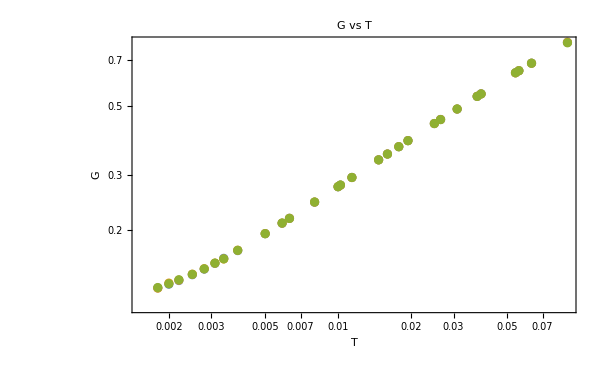

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]},{T,Length[Tlist]}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

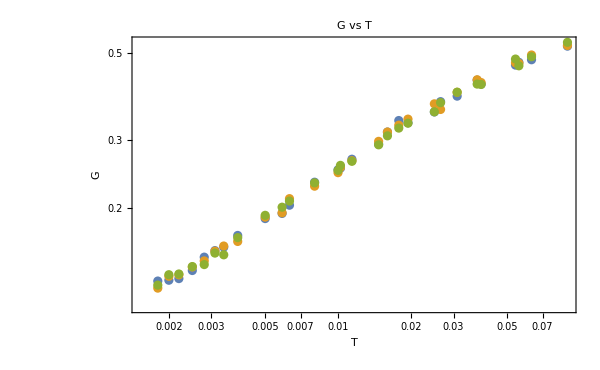

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g2s[[T,i]]},{T,Length[Tlist]}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

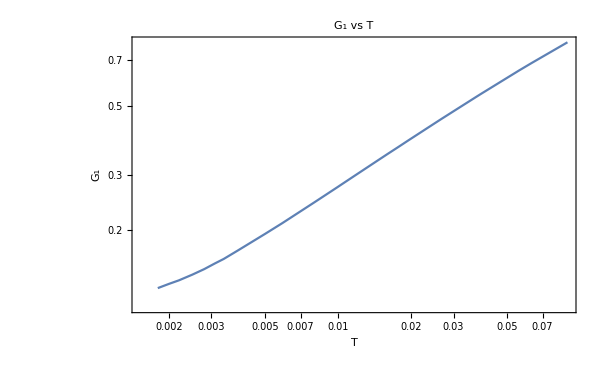

```mathematica
G1Plot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_1"},ImageSize->600,PlotLabel->"G_1 vs T",Joined->True]
```

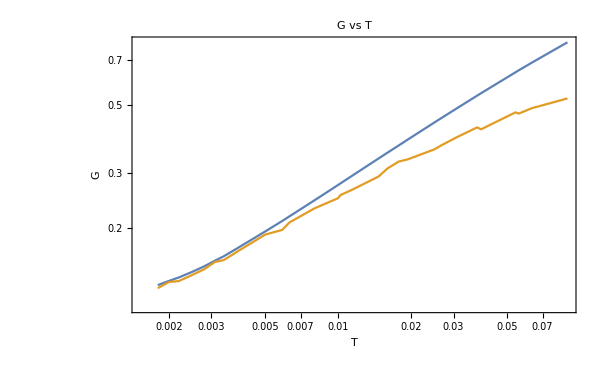

```mathematica
G2Plot=ListLogLogPlot[{Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],Table[{Tlist[[T]],g2[[T]]},{T,Length[Tlist]}]},FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T",Joined->True,PlotLabel->{"G_1,G_2"}]
```

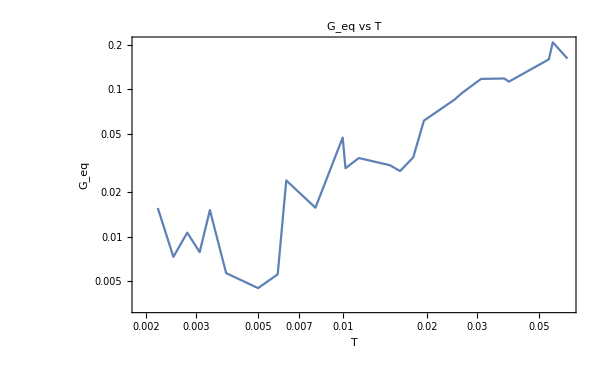

```mathematica
GeqPlot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_eq"},ImageSize->600,PlotLabel->"G_eq vs T",Joined->True]
```

### fitting

```mathematica
GT[A_,T_,B_]:=A T^B;
```

```mathematica
g1fitting=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[2.63248 t^0.487477]

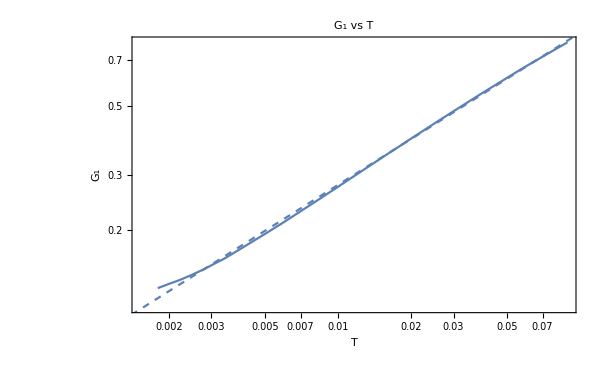

```mathematica
Show[G1Plot,LogLogPlot[g1fitting[x],{x,0.001,0.1},PlotStyle->Dashed]]
```

```mathematica
geqfitting=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[3.82428 t^1.07528]

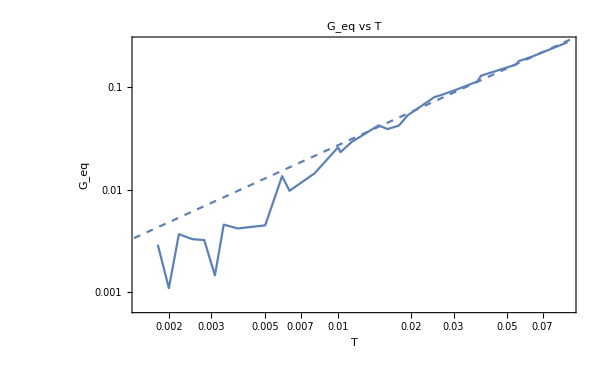

```mathematica
Show[GeqPlot,LogLogPlot[geqfitting[x],{x,0.001,0.1},PlotStyle->Dashed]]
```

```mathematica
G1380=Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}]
```

{{0.08868,0.798362},{0.063,0.684898},{0.05586,0.648017},{0.05409,0.638113},{0.039,0.546002},{0.03756,0.536114},{0.03105,0.488259},{0.02652,0.451782},{0.025,0.438584},{0.01945,0.386537},{0.01782,0.369611},{0.016,0.350087},{0.01471,0.33536},{0.01141,0.294386},{0.01023,0.27829},{0.01,0.275016},{0.008,0.245458},{0.0063,0.217645},{0.005873,0.210107},{0.005,0.194388},{0.00385,0.171792},{0.003371,0.161505},{0.0031,0.156259},{0.0028,0.149822},{0.0025,0.143833},{0.0022,0.137899},{0.002,0.134326},{0.0018,0.130233}}

```mathematica
Geq380=Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}]
```

{{0.08868,0.273277},{0.063,0.197195},{0.05586,0.179127},{0.05409,0.165011},{0.039,0.129045},{0.03756,0.113239},{0.03105,0.0948005},{0.02652,0.0830657},{0.025,0.0797422},{0.01945,0.0532957},{0.01782,0.041969},{0.016,0.0389017},{0.01471,0.0422693},{0.01141,0.0292098},{0.01023,0.0231413},{0.01,0.0257895},{0.008,0.0143807},{0.0063,0.00971294},{0.005873,0.0135011},{0.005,0.00446764},{0.00385,0.00416868},{0.003371,0.00454263},{0.0031,0.00145279},{0.0028,0.00320927},{0.0025,0.0032785},{0.0022,0.00366015},{0.002,0.00109064},{0.0018,0.00289308}}

```mathematica
G1385={{0.063,0.6417338019801752},{0.039,0.5216142405284101},{0.03105,0.4724795994316793},{0.025,0.4309465153947325},{0.016,0.35912629663509305},{0.01,0.302429070182306},{0.008,0.2816557750519702},{0.0063,0.2626501073850454},{0.005,0.2475155813857757},{0.00385,0.23365122986483153},{0.0031,0.22437067822650805},{0.0028,0.2206402895626671},{0.0025,0.21680949162466445},{0.0022,0.21295430796321066},{0.002,0.21031394819910867},{0.0018,0.20772417610010416},{0.001,0.19688942995882083},{0.00067,0.19191605897038824},{0.0005,0.1891403180512553},{0.0004,0.18739140348563454},{0.00033,0.18600106002776018},{0.00025,0.18429910951128026},{0.00018,0.18273899902570714},{0.00014,0.18152990806332794},{0.0001,0.18021821236495447}}
```

```mathematica
Geq385={{0.063,0.19451185935188114},{0.039,0.13190984285739704},{0.03105,0.10692888712561033},{0.025,0.08721358650737177},{0.016,0.0549537403633415},{0.01,0.03906085660185643},{0.008,0.032656222629975},{0.0063,0.019804237464172036},{0.005,0.02054883758024173},{0.00385,0.01338854201179096},{0.0031,0.011920864115745916},{0.0028,0.00897206571548681},{0.0025,0.010346795153061306},{0.0022,0.008360993834810926},{0.002,0.0066636095382197336},{0.0018,0.007187851910021165},{0.001,0.0045552409147564255},{0.00067,0.0008197157597248372},{0.0005,0.0016218729488757244},{0.0004,0.0023766576858079147},{0.00033,0.001479353937440142},{0.00025,0.0010705059966502894},{0.00018,0.0012431723201184464},{0.00014,0.00011295977499611864},{0.0001,0.0006270216438794274}}
```

```mathematica
G13825={{0.063,0.6616917986006604},{0.039,0.5313863446809616},{0.03105,0.47802717573034714},{0.025,0.4321974689732724},{0.016,0.3518893429441297},{0.01,0.28657322697368665},{0.008,0.26168153348912515},{0.0063,0.23921165625610633},{0.005,0.22084436283645018},{0.00385,0.20387459616126083},{0.0031,0.19245909070378106},{0.0028,0.18783573681984947},{0.0025,0.18312558450861424},{0.0022,0.17846820817414963},{0.002,0.17539422399197088},{0.0018,0.17230337327564302},{0.001,0.1604235920803833},{0.00067,0.15611101922363183},{0.0005,0.15405262019355917},{0.0004,0.15307784771644892},{0.00033,0.15248168885791527}}
```

{{0.063,0.661692},{0.039,0.531386},{0.03105,0.478027},{0.025,0.432197},{0.016,0.351889},{0.01,0.286573},{0.008,0.261682},{0.0063,0.239212},{0.005,0.220844},{0.00385,0.203875},{0.0031,0.192459},{0.0028,0.187836},{0.0025,0.183126},{0.0022,0.178468},{0.002,0.175394},{0.0018,0.172303},{0.001,0.160424},{0.00067,0.156111},{0.0005,0.154053},{0.0004,0.153078},{0.00033,0.152482}}

```mathematica
Geq3825={{0.063,0.19452598075423977},{0.039,0.13029891673087618},{0.03105,0.09798948978060185},{0.025,0.0796291045290275},{0.016,0.05570441520586744},{0.01,0.026554315067588208},{0.008,0.02423512921835852},{0.0063,0.01701214179207816},{0.005,0.012664951134567809},{0.00385,0.007766641974742167},{0.0031,0.007795943996065896},{0.0028,0.006780338906398342},{0.0025,0.005328962073321758},{0.0022,0.005584775284153576},{0.002,0.004526226483115597},{0.0018,0.003515902033444318},{0.001,0.003203944813387788},{0.00067,0.0015502818128856066},{0.0005,0.0024835221614595004},{0.0004,-0.0010904980919876628},{0.00033,0.0007414789443321024}}
```

{{0.063,0.194526},{0.039,0.130299},{0.03105,0.0979895},{0.025,0.0796291},{0.016,0.0557044},{0.01,0.0265543},{0.008,0.0242351},{0.0063,0.0170121},{0.005,0.012665},{0.00385,0.00776664},{0.0031,0.00779594},{0.0028,0.00678034},{0.0025,0.00532896},{0.0022,0.00558478},{0.002,0.00452623},{0.0018,0.0035159},{0.001,0.00320394},{0.00067,0.00155028},{0.0005,0.00248352},{0.0004,-0.0010905},{0.00033,0.000741479}}

```mathematica
f[x_]:=2.6324840539486676 x^0.4874774447876152;
```

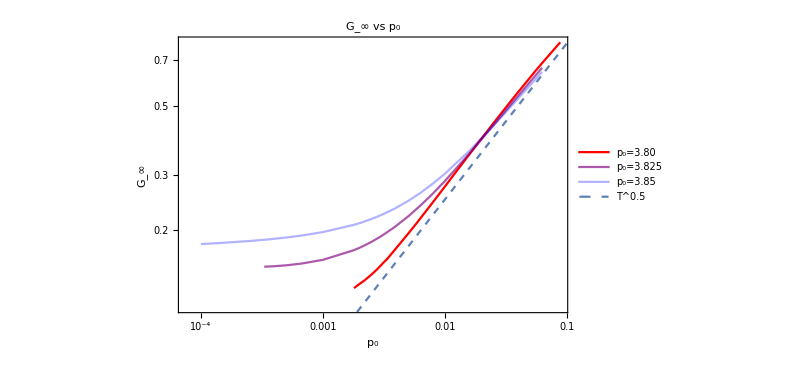

```mathematica
Show[ListLogLogPlot[{G1380,G13825,G1385},PlotLegends->{"p_0=3.80","p_0=3.825","p_0=3.85"},PlotStyle->redBluePlotConfig[3],FrameLabel->{"p_0","G_∞"},ImageSize->600,PlotLabel->"G_∞ vs p_0",Joined->True],LogLogPlot[2.5 x^0.5,{x,0.001,0.1},PlotStyle->Dashed,PlotLegends->{"T^0.5"}]]
```

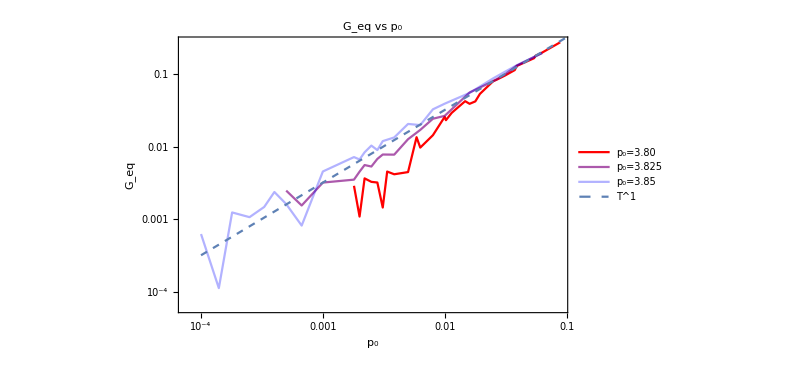

```mathematica
Show[ListLogLogPlot[{Geq380,Geq3825,Geq385},PlotLegends->{"p_0=3.80","p_0=3.825","p_0=3.85"},PlotStyle->redBluePlotConfig[3],FrameLabel->{"p_0","G_eq"},ImageSize->600,PlotLabel->"G_eq vs p_0",Joined->True],LogLogPlot[3.2 x^1,{x,0.0001,0.1},PlotStyle->Dashed,PlotLegends->{"T^1"}]]
```

```mathematica
∞
```

### G(t)=SACF*β*Area+Geq

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.00337100_waitingTime5times464.15_idx2.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
data[[2,130]]
```

2949.12

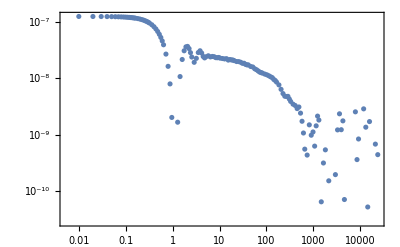

```mathematica
ListLogLogPlot[Table[{data[[2,t]],data[[1,t]]},{t,Length[data[[1]]]}],PlotRange->All]
```